```mathematica
(*Question 1*)
Clear["Global`*"]
P=2/5*bigN/V*EF[V]
```

(2 bigN EF[V])/(5 V)

```mathematica
-V*D[P,V]
```

```mathematica
-V (-(2 bigN EF[V])/(5 V^2)+(2 bigN EF'[V])/(5 V))/.EF'[V]->(-2/3*EF/V)
```

```mathematica
-V (-(4 bigN EF)/(15 V^2)-(2 bigN EF[V])/(5 V^2))/.EF[V]->EF
```

(2 bigN EF)/(3 V)

```mathematica
(*P*)
2/5*(0.00374)*(3.12)(*eV/A^3*)
Pval=2/5*(0.00374)*(3.12)*160.21766(*GPa*)
```

0.00466752

0.747819

```mathematica
(*B*)
2/3*(0.00374)*(3.12)(*eV/A^3*)
2/3*(0.00374)*(3.12)*160.21766(*GPa*)
5/3*Pval(*GPa*)
```

0.0077792

1.24637

1.24637

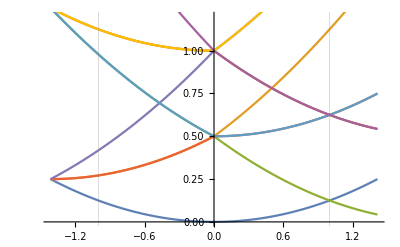

```mathematica
(*Question 2a*)
Clear["Global`*"]
k10[t_,h_,k_]:=(2π)/a{t/2+h,k}
k11[t_,h_,k_]:=(2π)/a{t/(2 √2)+h,t/(2 √2)+k}
EF10[t_,h_,k_]:=1/2((t/2+h)^2+k^2)
EF11[t_,h_,k_]:=1/2((t/(2 √2)+h)^2+(t/(2 √2)+k)^2)
Show[Plot[{EF11[t,0,0],EF11[t,1,0],EF11[t,-1,0],EF11[t,0,1],EF11[t,1,1],EF11[t,-1,1],EF11[t,0,-1],EF11[t,1,-1],EF11[t,-1,-1]},{t,-√2,0}],Plot[{EF10[t,0,0],EF10[t,1,0],EF10[t,-1,0],EF10[t,0,1],EF10[t,1,1],EF10[t,-1,1],EF10[t,0,-1],EF10[t,1,-1],EF10[t,-1,-1]},{t,0,√2}],PlotRange->{{-√2,√2},{0,1.2}},GridLines->{{-1,1},{}}]
```

```mathematica
(*2b*)
(*k vectors*)
k10[1,-1,-1]
k10[1,-1,0]
k10[1,-1,1]
k10[1,0,-1]
k10[1,0,0]
k10[1,0,1]
k10[1,1,-1]
k10[1,1,0]
k10[1,1,1]
```

{-π/a,-(2 π)/a}

{-π/a,0}

{-π/a,(2 π)/a}

{π/a,-(2 π)/a}

{π/a,0}

{π/a,(2 π)/a}

{(3 π)/a,-(2 π)/a}

{(3 π)/a,0}

{(3 π)/a,(2 π)/a}

```mathematica
(*Finding |k|*)
Norm[k10[1,-1,-1]]
Norm[k10[1,-1,0]]
Norm[k10[1,-1,1]]
Norm[k10[1,0,-1]]
Norm[k10[1,0,0]]
Norm[k10[1,0,1]]
Norm[k10[1,1,-1]]
Norm[k10[1,1,0]]
Norm[k10[1,1,1]]
```

(√5 π)/Abs[a]

π/Abs[a]

(√5 π)/Abs[a]

(√5 π)/Abs[a]

π/Abs[a]

(√5 π)/Abs[a]

(√13 π)/Abs[a]

(3 π)/Abs[a]

(√13 π)/Abs[a]

```mathematica
(*Checking out Evals*)
Norm[k10[1,-1,-1]]^2/(2(2π/Abs[a])^2)
Norm[k10[1,-1,0]]^2/(2(2π/Abs[a])^2)
Norm[k10[1,-1,1]]^2/(2(2π/Abs[a])^2)
Norm[k10[1,0,-1]]^2/(2(2π/Abs[a])^2)
Norm[k10[1,0,0]]^2/(2(2π/Abs[a])^2)
Norm[k10[1,0,1]]^2/(2(2π/Abs[a])^2)
Norm[k10[1,1,-1]]^2/(2(2π/Abs[a])^2)
Norm[k10[1,1,0]]^2/(2(2π/Abs[a])^2)
Norm[k10[1,1,1]]^2/(2(2π/Abs[a])^2)
```

5/8

1/8

5/8

5/8

1/8

5/8

13/8

9/8

13/8

```mathematica
(*Evals we check our k's against*)
EF10[1,-1,-1]
EF10[1,-1,0]
EF10[1,-1,1]
EF10[1,0,-1]
EF10[1,0,0]
EF10[1,0,1]
EF10[1,1,-1]
EF10[1,1,0]
EF10[1,1,1]
```

5/8

1/8

5/8

5/8

1/8

5/8

13/8

9/8

13/8

```mathematica
(*Finding λ =2π/|k|*)
2*π/Norm[k10[1,-1,-1]]
2*π/Norm[k10[1,-1,0]]
2*π/Norm[k10[1,-1,1]]
2*π/Norm[k10[1,0,-1]]
2*π/Norm[k10[1,0,0]]
2*π/Norm[k10[1,0,1]]
2*π/Norm[k10[1,1,-1]]
2*π/Norm[k10[1,1,0]]
2*π/Norm[k10[1,1,1]]
```

(2 Abs[a])/(√5)

2 Abs[a]

(2 Abs[a])/(√5)

(2 Abs[a])/(√5)

2 Abs[a]

(2 Abs[a])/(√5)

(2 Abs[a])/(√13)

(2 Abs[a])/3

(2 Abs[a])/(√13)

```mathematica
(*2c*)
k10vec=(2π)/a{(t/2+h),k};
k11vec=(2π)/a{(t/(2 √2)+h),(t/(2 √2)+k)};
Gvec10=(2π)/a{1,0};
Gvec11=(2π)/a{1/(√2),1/(√2)};
Ghat10={1,0};
Ghat11={1/(√2),1/(√2)};
k10vec.Ghat10
-Norm[Gvec10]/2
k11vec.Ghat11
-Norm[Gvec11]/2

FullSimplify[Solve[(2 π^2)/a^2(h+k)==-π/a(h^2+k^2),{h,k}]]
```

(2 π (h+t/2))/a

-π/Abs[a]

(√2 π (h+t/(2 √2)))/a+(√2 π (k+t/(2 √2)))/a

-π/Abs[a]

Solve::svars: Equations may not give solutions for all "solve" variables.

{{k→-(π+√(-a^2 h^2-2 a h π+π^2))/a},{k→(-π+√(-a^2 h^2-2 a h π+π^2))/a}}

```mathematica
(*Question 3*)
2*π*kf^2/(2π/L)^2
```

(kf^2 L^2)/(2 π)

```mathematica
N[√(2/π)]
N[2/√π]
N[√(6/π)]
N[√2]
```

0.797885

1.12838

1.38198

1.41421